# MMA 绘图

## Manipulate 使用

### 4.1 基本操作

```mathematica
Manipulate[
Plot[A Sin[a x], {x, -5, 5},
	PlotRange->{{-5, 5}, {-5, 5}}
	],
	{a, 2, 5, 0.5},
	{A, -2, 2, 0.2}
]
```

### 4.2 多个参数

```mathematica
Manipulate[
	Plot[function[frequency*x+phase], {x, 0, 2π}],
		{frequency, 1, 5},
		{phase, 1, 10},
		{function, {Sin, Cos, Tan, Csc, Sec, Cot},
		ControlType->RadioButtonBar}
]
```

### 4.3 Taylor公式逼近模拟

```mathematica
Animate[Plot[Evaluate[{Sin[x], Normal[Series[Sin[x], {x,0,n}]]}],
	{x,-5,5},
	PlotRange->5,
	AspectRatio->1,
	PlotLegends->"Expressions"],
	{n,1,20,2}
]
```

### 4.4 图例显示

```mathematica
Manipulate[With[
	{value=a}, 
	Plot[Sin[value x],
		{x,0,10},
		PlotLegends->"AllExpressions"
	]],
	{a,1,2}
]
```

### 4.3 Fourier级数模拟

1/2-2/Pi*

```mathematica
Manipulate[(*错误的函数：f=Sum[Sin[(2k+1) x]/(2k+1),{k,1,n}];*)f=Sum[((-1)^k-1)/k Sin[k x],{k,1,n}];
g = Which[-Pi<x<0,1,0<=x<Pi,0];
h = 1/2 + 1/π*f;
Plot[{g, h}, 
	{x, -Pi, Pi}, 
	PlotStyle->{Blue, Red},
	PlotRange->{-0.2, 1.5},
	PlotLegends->"AllExpressions"],
	{n, 1, 100}
]
```

检验傅里叶级数展开的和式

```mathematica
Manipulate[f=Sum[Sin[(2k+1) x]/(2k+1),{k,1,n}],{n,1,5}]
```

关于的展开

```mathematica
Manipulate[f1=Sum[((-1)^k-1)/k^2 Cos[k x],{k,1,n}];
(*f1 只包含了Subscript[a,n],f2只包含了Subscript[b,n]*)f2=Sum[(-1)^(k+1)/k*Sin[k x],{k,1,n}];
g=x;
h1=π/2+2/π*f1;
h2=2*f2;
Plot[{g, h1, h2},
	{x, -Pi-0.5, Pi+0.5},
	PlotStyle->{Blue, Red, Green},
	PlotRange->{Automatic, Automatic},
	PlotLegends->"AllExpressions",
	AxesLabel->{x, y},
	AxesStyle->Arrowheads[{0, 0.03}]],{n, 1, 100}]
```

### 4.5 函数项级数的误差累计项

```mathematica
Manipulate[
Plot[
n x (1-x^2)^n,{x, -5, 5},
PlotRange->{-10, 10},
PlotStyle->{Red},
AxesLabel->{x, y},
AxesStyle->Arrowheads[{0,0.03}]
],
{n, 1, 50}]
```

## 6. 子图的功能

```mathematica
p1 = Plot[x Sin[x] - 1, {x, -2.5, 2.5}];
p2 = Plot[Evaluate[D[x Sin[x] - 1, x]], {x, -2.5, 2.5}, PlotStyle -> Red];
p3 = Plot[Sin[x], {x, -2.5, 2.5}, PlotStyle -> Magenta];
p4 = Graphics[{Magenta, Polygon[{{0.4, 0}, {0, 0.5}, {-0.4, 0}}]}];
```

### 图形的叠加

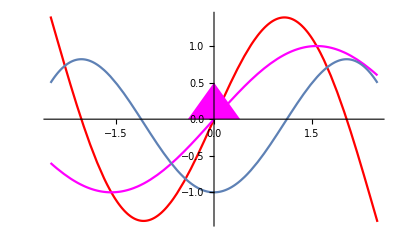

```mathematica
Show[p2, p3, p1, p4]
```

### 排列为一行/列

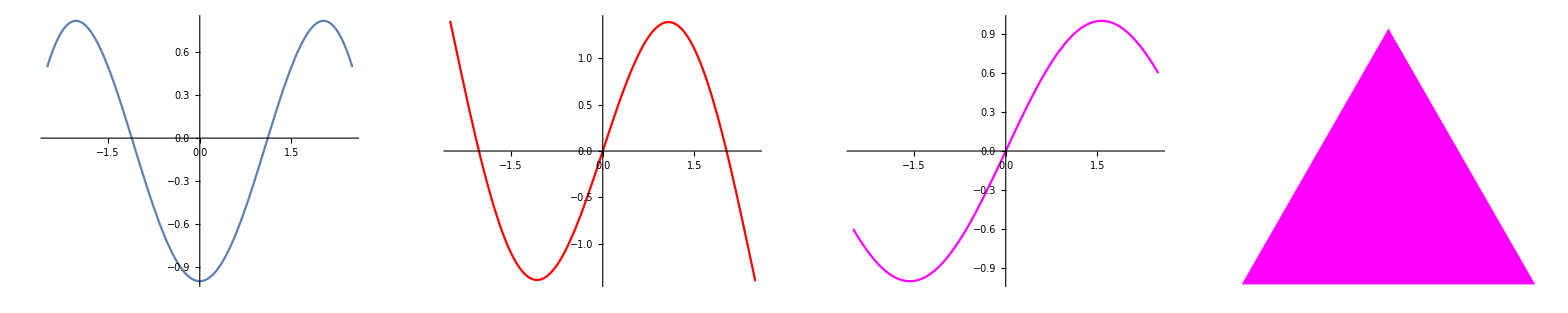

```mathematica
GraphicsRow[{p1, p2, p3, p4}]
```

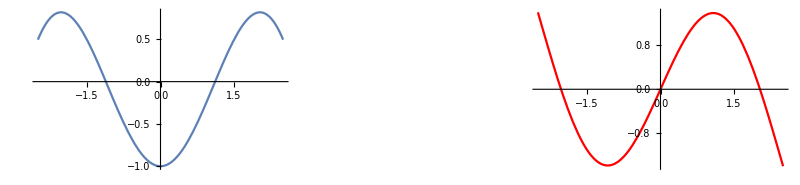

```mathematica
GraphicsGrid[{{p1,p2}},Spacings -> {Scaled[1], Scaled[0]}]
(*可以通过设置选项Spacings->{h,v} 改变边缘的大小.*)
```

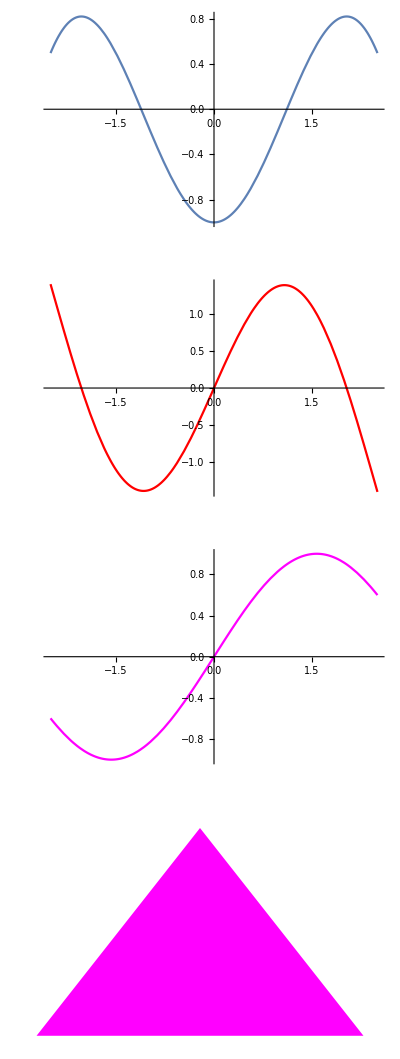

```mathematica
GraphicsColumn[{p1, p2, p3, p4}]
```

### 排列为一个矩阵

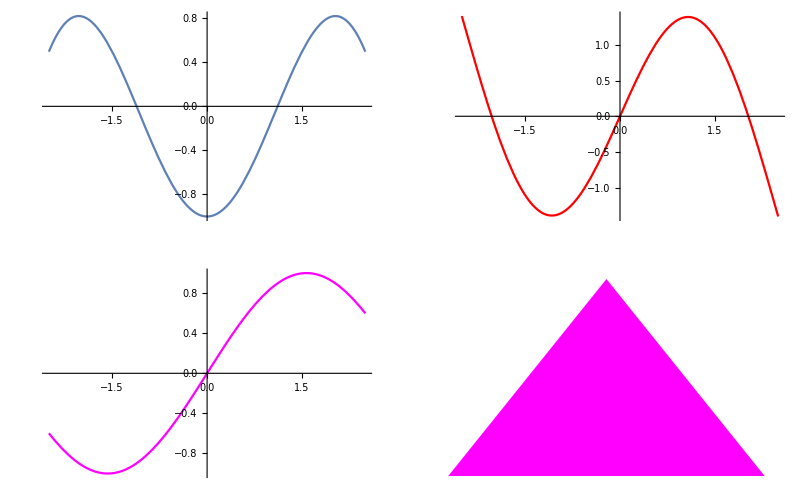

```mathematica
GraphicsGrid[{{p1, p2}, {p3, p4}}]
```